We consider the eigenvalue filtering function from Lin and Tong 2020, “optimal poly...qls”. Δ, ϵ. α are considered set by the user, and the degree and polynomial and computed from them. We assume $\epsilon\in(0,1)$ and $\Delta\in(0, 1/\sqrt{12}]$ are given by the user. For simplicity we set α=1 and ignore the block encoding.

```mathematica
$myPrecision=6(*N[64*Log10[2]]*);
myN[x_]:=N[x,$myPrecision];
myP[x_]:=SetPrecision[x,$myPrecision];
```

```mathematica
k[Δ_, ϵ_]:=myP[Ceiling[Log[2/ϵ]/Δ/Sqrt[2]]];
flt20[x_, Δ_, ϵ_]:=myP[ChebyshevT[k[Δ, ϵ],-1+2*(x^2-Δ^2)/(1-Δ^2)]/ChebyshevT[k[Δ, ϵ],-1+2*(-Δ^2)/(1-Δ^2)]];
flt20shft[x_, Δ_, α_, ϵ_]:=myP[flt20[x, Δ/2/α, ϵ]];
```

We first plot the possible values of the degree (actually, 1/2 of the degree) to determine the order of magnitude needed for realistic calculations.

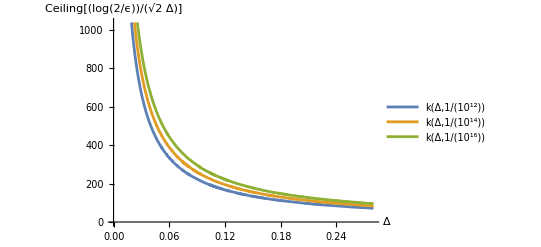

```mathematica
Plot[{k[Δ, 10^(-12)], k[Δ, 10^(-14)], k[Δ, 10^(-16)]}, {Δ, 0, 0.28}, PlotLegends->"Expressions",AxesLabel->{Δ, k[Δ, ϵ]} ]
```

Next we want to check how the function behaves for $x\in[0, 1]$ in these ‘realistic’ range
s: the Δ range and ϵ=10^(-12) values given in Dong et al 2021 “efficient...”

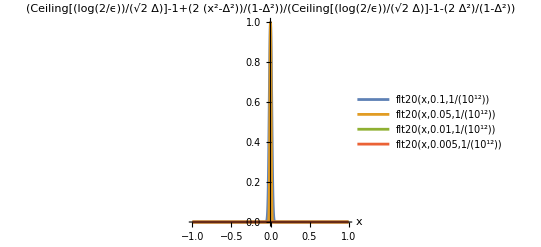

```mathematica
Plot[{flt20[x, 0.1, 10^(-12)], flt20[x, 0.05, 10^(-12)], flt20[x, 0.01, 10^(-12)], flt20[x, 0.005, 10^(-12)]}, {x, -1, 1}, PlotLegends->"Expressions", AxesLabel->{x, flt20[x, Δ, ϵ]}, PlotRange->Full]
```

Try  a very restricted domain to pick out the ‘nontrivial’ function behaviour, We don’t care if it quickly goes to zero, yeah?

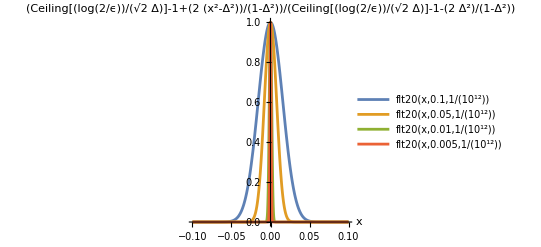

```mathematica
Plot[{flt20[x, 0.1, 10^(-12)], flt20[x, 0.05, 10^(-12)], flt20[x, 0.01, 10^(-12)], flt20[x, 0.005, 10^(-12)]}, {x, -0.1, 0.1}, PlotLegends->"Expressions", AxesLabel->{x, flt20[x, Δ, ϵ]}, PlotRange->Full]
```

So this very quickly becomes an approximation of the Dirac Delta function?

Now for convenience, we want a version of this that adjusts for shift $\Delta\rightarrow \Tilde{\Delta}$

```mathematica
Plot[{flt20[x, 0.1, 10^(-12)], flt20[x, 0.05, 10^(-12)], flt20[x, 0.01, 10^(-12)], flt20[x, 0.005, 10^(-12)]}, {x, -0.1, 0.1}, PlotLegends->"Expressions", AxesLabel->{x, flt20[x, Δ, ϵ]}, PlotRange->Full]
```

-Graphics-

Okay great no weird changes - now we want to extract coefficient lists

```mathematica
delt1=0.4;
alph1=1;
epsi1=10^(-6);
```

```mathematica
A=flt20shft[0.1,delt1, alph1,epsi1 ];
```

```mathematica
Precision[A]
```

6.

```mathematica
L1=CoefficientList[flt20shft[x, delt1, alph1, epsi1], {x}];
```

```mathematica
Plot[x^(Range[0, Length[L1]-1]).L1-flt20shft[x,delt1, alph1,epsi1 ], {x, -1, 1}, PlotRange->Full]
```

-Graphics-

```mathematica
nlt=Ceiling[2*k[delt1/2, epsi1]]
F2:=Expand[flt20shft[x, delt1, alph1, epsi1]]/.x->(z+z^(-1))/2;
LaurentList=myN[CoefficientList[Expand[z^nlt*F2], {z}]];
A=Partition[LaurentList,2,2,1,{}]~Flatten~{2};
LeadingList=Riffle[A[[1]], 0, 2];
NonleadingList=Riffle[A[[2]], 0, {1, 2*nlt+1, 2}];
OddList=If[EvenQ[nlt]==True, NonleadingList, LeadingList];
EvenList=If[EvenQ[nlt]==True, LeadingList, NonleadingList];
```

54

```mathematica
LaurentList
```

{-0.0150264,0,0.00159655,0,-0.00167987,0,0.00176504,0,-0.00185203,0,0.00194078,0,-0.0020318,0,0.00210571,0,-0.00390625,0,-0.09375,0,-4.67188,0,-46.,0,-1088.,0,-47104.,0,-1.31072×10^6,0,-1.25829×10^7,0,-3.35544×10^8,0,-5.36871×10^9,0,-8.58993×10^10,0,-1.64927×10^12,0,-2.19902×10^13,0,-1.77587×10^14,0,-1.89363×10^15,0,-1.62827×10^16,0,-2.60083×10^17,0,-4.534×10^18,0,-2.58957×10^19,0,-3.70952×10^20,0,-3.51872×10^21,0,-7.3787×10^21,0,-1.47574×10^23,0,-1.76617×10^24,0,-8.23581×10^24,0,-5.31927×10^25,0,-3.77185×10^26,0,-2.63062×10^27,0,-2.1045×10^28,0,-9.16076×10^28,0,-2.77299×10^29,0,-2.05993×10^30,0,-1.01412×10^31,0,-4.56354×10^31,0,-2.43389×10^32,0,-9.78854×10^32,0,-4.41725×10^33,0,-1.01073×10^34,0,-3.20017×10^34,0,1.37402×10^35,0,8.69212×10^34,0,4.80311×10^36,0,1.18176×10^37,0,3.75287×10^37,0,2.40238×10^38,0,7.32142×10^38,0,3.05655×10^39,0,7.27001×10^39,0,2.399×10^40,0,8.29356×10^40,0,2.24217×10^41,0,6.38388×10^41,0,1.59423×10^42,0,4.02245×10^42,0,8.82963×10^42,0,1.91538×10^43,0,4.64043×10^43,0,8.84309×10^43,0,1.80957×10^44,0,3.70683×10^44,0,6.82049×10^44,0,1.20421×10^45,0,2.02319×10^45,0,3.66169×10^45,0,5.36228×10^45,0,8.83997×10^45,0,1.30861×10^46,0,1.95938×10^46,0,2.61123×10^46,0,3.53785×10^46,0,4.50218×10^46,0,5.75751×10^46,0,6.89445×10^46,0,8.37109×10^46,0,9.28609×10^46,0,1.00109×10^47,0,1.12429×10^47,0,1.07405×10^47,0,1.12429×10^47,0,1.00109×10^47,0,9.28609×10^46,0,8.37109×10^46,0,6.89445×10^46,0,5.75751×10^46,0,4.50218×10^46,0,3.53785×10^46,0,2.61123×10^46,0,1.95938×10^46,0,1.30861×10^46,0,8.83997×10^45,0,5.36228×10^45,0,3.66169×10^45,0,2.02319×10^45,0,1.20421×10^45,0,6.82049×10^44,0,3.70683×10^44,0,1.80957×10^44,0,8.84309×10^43,0,4.64043×10^43,0,1.91538×10^43,0,8.82963×10^42,0,4.02245×10^42,0,1.59423×10^42,0,6.38388×10^41,0,2.24217×10^41,0,8.29356×10^40,0,2.399×10^40,0,7.27001×10^39,0,3.05655×10^39,0,7.32142×10^38,0,2.40238×10^38,0,3.75287×10^37,0,1.18176×10^37,0,4.80311×10^36,0,8.69212×10^34,0,1.37402×10^35,0,-3.20017×10^34,0,-1.01073×10^34,0,-4.41725×10^33,0,-9.78854×10^32,0,-2.43389×10^32,0,-4.56354×10^31,0,-1.01412×10^31,0,-2.05993×10^30,0,-2.77299×10^29,0,-9.16076×10^28,0,-2.1045×10^28,0,-2.63062×10^27,0,-3.77185×10^26,0,-5.31927×10^25,0,-8.23581×10^24,0,-1.76617×10^24,0,-1.47574×10^23,0,-7.3787×10^21,0,-3.51872×10^21,0,-3.70952×10^20,0,-2.58957×10^19,0,-4.534×10^18,0,-2.60083×10^17,0,-1.62827×10^16,0,-1.89363×10^15,0,-1.77587×10^14,0,-2.19902×10^13,0,-1.64927×10^12,0,-8.58993×10^10,0,-5.36871×10^9,0,-3.35544×10^8,0,-1.25829×10^7,0,-1.31072×10^6,0,-47104.,0,-1088.,0,-46.,0,-4.67188,0,-0.09375,0,-0.00390625,0,0.00210571,0,-0.0020318,0,0.00194078,0,-0.00185203,0,0.00176504,0,-0.00167987,0,0.00159655,0,-0.0150264}

```mathematica
CoefficientList[z^nlt*Expand[flt20shft[x, delt1, alph1, epsi1]]/.x->(z+z^(-1))/2, {z}]
```

{-0.0180126,0,0.0202641,0,-0.029763,0,0.0403964,0,-0.051489,0,0.0622281,0,-0.0717495,0,0.0792378,0,-0.0840243,0,0.0856707,0,-0.0840243,0,0.0792378,0,-0.0717495,0,0.0622281,0,-0.051489,0,0.0403964,0,-0.029763,0,0.0202641,0,-0.0180126}

```mathematica
L1=CoefficientList[flt20shft[x, delt1, alph1, epsi1], {x}]
```

{1.,0,-135.,0,8235.,0,-302445.,0,7.52355×10^6,0,-1.35272×10^8,0,1.83244×10^9,0,-1.92512×10^10,0,1.60229×10^11,0,-1.07379×10^12,0,5.86721×10^12,0,-2.63941×10^13,0,9.84878×10^13,0,-3.06516×10^14,0,7.98653×10^14,0,-1.74591×10^15,0,3.20377×10^15,0,-4.92876×10^15,0,6.33701×10^15,0,-6.77258×10^15,0,5.96733×10^15,0,-4.28337×10^15,0,2.46226×10^15,0,-1.10556×10^15,0,3.73316×10^14,0,-8.91191×10^13,0,1.34029×10^13,0,-9.54624×10^11}

```mathematica
LaurentList
```

{-0.0180126,0,0.0202641,0,-0.029763,0,0.0403964,0,-0.051489,0,0.0622281,0,-0.0717495,0,0.0792378,0,-0.0840243,0,0.0856707,0,-0.0840243,0,0.0792378,0,-0.0717495,0,0.0622281,0,-0.051489,0,0.0403964,0,-0.029763,0,0.0202641,0,-0.0180126}

```mathematica
LeadingList
```

{-0.0150536,0,0.00323653,0,-0.00357232,0,0.00392241,0,-0.00428624,0,0.00466318,0,-0.00505254,0,0.00545287,0,-0.00587463,0,0.00604248,0,-0.00976563,0,-0.0184631,0,-0.311523,0,-1.3125,0,-28.,0,-192.,0,-832.,0,-4096.,0,-32768.,0,98304.,0,-1.04858×10^6,0,2.09715×10^6,0,1.28909×10^7,0,-7.64546×10^6,0,2.88225×10^7,0,1.1518×10^9,0,3.13829×10^9,0,6.57116×10^9,0,-1.37301×10^10,0,-4.5072×10^10,0,-7.68396×10^9,0,-1.44821×10^11,0,-1.12474×10^11,0,-1.09092×10^12,0,-5.8884×10^12,0,-1.24941×10^13,0,-1.8958×10^13,0,-3.49267×10^13,0,-6.09542×10^13,0,-1.17991×10^14,0,-1.98531×10^14,0,-1.58948×10^14,0,-1.91315×10^14,0,-2.31447×10^14,0,-1.91315×10^14,0,-1.58948×10^14,0,-1.98531×10^14,0,-1.17991×10^14,0,-6.09542×10^13,0,-3.49267×10^13,0,-1.8958×10^13,0,-1.24941×10^13,0,-5.8884×10^12,0,-1.09092×10^12,0,-1.12474×10^11,0,-1.44821×10^11,0,-7.68396×10^9,0,-4.5072×10^10,0,-1.37301×10^10,0,6.57116×10^9,0,3.13829×10^9,0,1.1518×10^9,0,2.88225×10^7,0,-7.64546×10^6,0,1.28909×10^7,0,2.09715×10^6,0,-1.04858×10^6,0,98304.,0,-32768.,0,-4096.,0,-832.,0,-192.,0,-28.,0,-1.3125,0,-0.311523,0,-0.0184631,0,-0.00976563,0,0.00604248,0,-0.00587463,0,0.00545287,0,-0.00505254,0,0.00466318,0,-0.00428624,0,0.00392241,0,-0.00357232,0,0.00323653,0,-0.0150536}

{0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.}

```mathematica
Re[(ⅇ^(ⅈ*θ))^Range[-nlt,nlt].LeadingList]
```

-2.31447×10^14+Re[-1.91315×10^14 ⅇ^(-2 ⅈ θ)-1.91315×10^14 ⅇ^(2 ⅈ θ)-1.58948×10^14 ⅇ^(-4 ⅈ θ)-1.58948×10^14 ⅇ^(4 ⅈ θ)-1.98531×10^14 ⅇ^(-6 ⅈ θ)-1.98531×10^14 ⅇ^(6 ⅈ θ)-1.17991×10^14 ⅇ^(-8 ⅈ θ)-1.17991×10^14 ⅇ^(8 ⅈ θ)-6.09542×10^13 ⅇ^(-10 ⅈ θ)-6.09542×10^13 ⅇ^(10 ⅈ θ)-3.49267×10^13 ⅇ^(-12 ⅈ θ)-3.49267×10^13 ⅇ^(12 ⅈ θ)-1.8958×10^13 ⅇ^(-14 ⅈ θ)-1.8958×10^13 ⅇ^(14 ⅈ θ)-1.24941×10^13 ⅇ^(-16 ⅈ θ)-1.24941×10^13 ⅇ^(16 ⅈ θ)-5.8884×10^12 ⅇ^(-18 ⅈ θ)-5.8884×10^12 ⅇ^(18 ⅈ θ)-1.09092×10^12 ⅇ^(-20 ⅈ θ)-1.09092×10^12 ⅇ^(20 ⅈ θ)-1.12474×10^11 ⅇ^(-22 ⅈ θ)-1.12474×10^11 ⅇ^(22 ⅈ θ)-1.44821×10^11 ⅇ^(-24 ⅈ θ)-1.44821×10^11 ⅇ^(24 ⅈ θ)-7.68396×10^9 ⅇ^(-26 ⅈ θ)-7.68396×10^9 ⅇ^(26 ⅈ θ)-4.5072×10^10 ⅇ^(-28 ⅈ θ)-4.5072×10^10 ⅇ^(28 ⅈ θ)-1.37301×10^10 ⅇ^(-30 ⅈ θ)-1.37301×10^10 ⅇ^(30 ⅈ θ)+6.57116×10^9 ⅇ^(-32 ⅈ θ)+6.57116×10^9 ⅇ^(32 ⅈ θ)+3.13829×10^9 ⅇ^(-34 ⅈ θ)+3.13829×10^9 ⅇ^(34 ⅈ θ)+1.1518×10^9 ⅇ^(-36 ⅈ θ)+1.1518×10^9 ⅇ^(36 ⅈ θ)+2.88225×10^7 ⅇ^(-38 ⅈ θ)+2.88225×10^7 ⅇ^(38 ⅈ θ)-7.64546×10^6 ⅇ^(-40 ⅈ θ)-7.64546×10^6 ⅇ^(40 ⅈ θ)+1.28909×10^7 ⅇ^(-42 ⅈ θ)+1.28909×10^7 ⅇ^(42 ⅈ θ)+2.09715×10^6 ⅇ^(-44 ⅈ θ)+2.09715×10^6 ⅇ^(44 ⅈ θ)-1.04858×10^6 ⅇ^(-46 ⅈ θ)-1.04858×10^6 ⅇ^(46 ⅈ θ)+98304. ⅇ^(-48 ⅈ θ)+98304. ⅇ^(48 ⅈ θ)-32768. ⅇ^(-50 ⅈ θ)-32768. ⅇ^(50 ⅈ θ)-4096. ⅇ^(-52 ⅈ θ)-4096. ⅇ^(52 ⅈ θ)-832. ⅇ^(-54 ⅈ θ)-832. ⅇ^(54 ⅈ θ)-192. ⅇ^(-56 ⅈ θ)-192. ⅇ^(56 ⅈ θ)-28. ⅇ^(-58 ⅈ θ)-28. ⅇ^(58 ⅈ θ)-1.3125 ⅇ^(-60 ⅈ θ)-1.3125 ⅇ^(60 ⅈ θ)-0.311523 ⅇ^(-62 ⅈ θ)-0.311523 ⅇ^(62 ⅈ θ)-0.0184631 ⅇ^(-64 ⅈ θ)-0.0184631 ⅇ^(64 ⅈ θ)-0.00976563 ⅇ^(-66 ⅈ θ)-0.00976563 ⅇ^(66 ⅈ θ)+0.00604248 ⅇ^(-68 ⅈ θ)+0.00604248 ⅇ^(68 ⅈ θ)-0.00587463 ⅇ^(-70 ⅈ θ)-0.00587463 ⅇ^(70 ⅈ θ)+0.00545287 ⅇ^(-72 ⅈ θ)+0.00545287 ⅇ^(72 ⅈ θ)-0.00505254 ⅇ^(-74 ⅈ θ)-0.00505254 ⅇ^(74 ⅈ θ)+0.00466318 ⅇ^(-76 ⅈ θ)+0.00466318 ⅇ^(76 ⅈ θ)-0.00428624 ⅇ^(-78 ⅈ θ)-0.00428624 ⅇ^(78 ⅈ θ)+0.00392241 ⅇ^(-80 ⅈ θ)+0.00392241 ⅇ^(80 ⅈ θ)-0.00357232 ⅇ^(-82 ⅈ θ)-0.00357232 ⅇ^(82 ⅈ θ)+0.00323653 ⅇ^(-84 ⅈ θ)+0.00323653 ⅇ^(84 ⅈ θ)-0.0150536 ⅇ^(-86 ⅈ θ)-0.0150536 ⅇ^(86 ⅈ θ)]

```mathematica
CList=Prepend[EvenList/2, "C"];
SList=Prepend[OddList/2, "S"];
nList=Prepend[Table[nlt, {i, 1, nlt*2+1}], "n"];
```

```mathematica
Export["C:\\Users\\skelt\\Documents\\GitHub\\QSVT\\csv_files\\flt_delta_005_epsi_1.csv",Transpose[{CList, SList, nList}], "CSV" ]
```

C:\Users\skelt\Documents\GitHub\QSVT\csv_files\flt_delta_005_epsi_1.csv

```mathematica
Plot[Re[(ⅇ^(ⅈ*θ*Range[-nlt, nlt]).LeadingList)], {θ, 0, π}]
```

-Graphics-

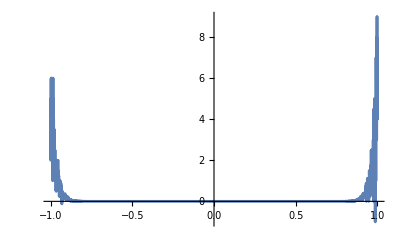

```mathematica
Plot[x^(Range[0, Length[L1]-1]).L1-flt20shft[x,delt1, alph1,epsi1 ], {x, -1, 1}, PlotRange->Full]
```

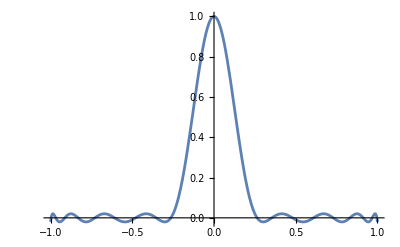

```mathematica
Plot[flt20shft[x,delt1, alph1,epsi1 ], {x, -1, 1}, PlotRange->Full]
```

```mathematica
Simplify[x^(Range[0, nlt]).L1,-flt20shft[x,delt1, alph1,epsi1 ]]/.x-> 0.3
```

5.81766×10^18

```mathematica
Plot[flt20shft[ⅇ^(ⅈ*ArcCos[x])/2+ⅇ^(-ⅈ*ArcCos[x])/2,delt1, alph1,epsi1 ], {x,-1, 1}]
```

-0.0284974 (85. (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))-102340. (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^3+3.69243×10^7 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^5-6.32988×10^9 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^7+6.30878×10^11 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^9-4.09726×10^13 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^11+1.86583×10^15 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^13-6.26919×10^16 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^15+1.61339×10^18 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^17-3.27208×10^19 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^19+5.34751×10^20 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^21-7.16947×10^21 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^23+8.00113×10^22 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^25-7.52243×10^23 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^27+6.01794×10^24 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^29-4.13103×10^25 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^31+2.45045×10^26 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^33-1.26353×10^27 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^35+5.69156×10^27 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^37-2.24897×10^28 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^39+7.82203×10^28 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^41-2.40118×10^29 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^43+6.51957×10^29 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^45-1.56807×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^47+3.34416×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^49-6.32636×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^51+1.06143×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^53-1.57821×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^55+2.07659×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^57-2.41278×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^59+2.46816×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^61-2.21414×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^63+1.73299×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^65-1.1757×10^31 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^67+6.85577×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^69-3.39892×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^71+1.41234×10^30 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^73-4.82485×10^29 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^75+1.31916×10^29 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^77-2.77448×10^28 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^79+4.21311×10^27 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^81-4.11035×10^26 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^83+1.93428×10^25 (-1.+2.00125 (-0.000625+(0.5/z+0.5 z)^2))^85)

```mathematica
(*Chebybasis[x_, k_]:=Table[ChebyshevJ[j, x],{j,0,2*k}];*)
(*CPlt19[Δ_, ϵ_]:=Collect[flt20shft[x, Δ, ϵ], possvars[x, k[Δ/2, ϵ]]]*)
(*Pshftlist[Δ_, ϵ_]:=Table[FourierCoefficient[flt20shft[x, Δ, ϵ], x, j],{j, 0, 2*k[Δ/2, ϵ]}];*)
CPlt19[Δ_, ϵ_]:=SolveAlways[Simplify[flt20shft[x, Δ, ϵ]]==Table[C[i],{i,0,2*k[Δ/2, ϵ]}].Chebybasis[x, k[Δ/2, ϵ]],x];
CPlt19[0.4, 10^(-3)]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -6281274941308525+847972116567769856 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^2-51726299146036436992 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^4+1899740197995402756096 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^6-47257486116721858183168 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^8+849679930873899344986112 («1»)^10-11510064349020538913423360 (InverseFunction[ChebyshevJ,2,2][54,«1»])^12+120922180283774876021424128 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^14-1006445099483389994702209024 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^16+6744759855974163228645130240 (InverseFunction[ChebyshevJ,2,2][54,ChebyshevJ[54,x]])^18+«18» == 0.

SolveAlways::ifun: Inverse functions are being used by SolveAlways, so some solutions may not be found; use Reduce for complete solution information.

Try a different method for building coefficients

```mathematica
δ=0.1;
ϵ=10^(-6);
```

```mathematica
Simplify[ChebyshevT[4,-1+2*(x^2-(δ/2)^2)/(1-(δ/2)^2)]]
(*Collect[ChebyshevT[4,-1+2*(x^2-(δ/2)^2)/(1-(δ/2)^2)],ChebyshevJ[_, x]]*)
CoefficientRules[ChebyshevT[4,-1+2*(x^2-(δ/2)^2)/(1-(δ/2)^2)], {1, x, 2x^2-1, 4*x^3-3*x, 8*x^4-8*x^2+1}]
```

1.08121-32.8891 x^2+162.742 x^4-259.223 x^6+129.288 x^8

General::ivar: 1-8 x^2+8 x^4 is not a valid variable.

CoefficientRules[1.-8. (-1.+2.00501 (-0.0025+x^2))^2+8. (-1.+2.00501 (-0.0025+x^2))^4,{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4}]

```mathematica
StringJoin["flt20shft_Delta_is_",ToString[0.4],"_epsi_is_",ToString[0.2]]
```

flt20shft_Delta_is0.4_epsi_is_0.2

```mathematica
GetCoeffs[Δ_, ϵ_]:=Export[StringJoin["C:\\Users\\skelt\\OneDrive\\Documents\\GitHub\\QSVT\\csv_files\\", "flt20shft_Delta_is_",ToString[Δ],"_epsipow_is_",ToString[-Log10[ϵ]], ".csv"],Pshftlist[Δ, ϵ],"CSV"]
```

```mathematica
GetCoeffs[0.3, 10^(-12)]
```

C:\Users\skelt\OneDrive\Documents\GitHub\QSVT\csv_files\flt20shft_Delta_is_0.3_epsipow_is_12.csv

None of the simplifications in mathematica have been good at simplifying a polynomial wrt a Chebyshev series, and I don’t want to have to take Fourier series. So let”s try some polynomial interpolation

```mathematica
testfcn[x_, Δ_, ϵ_]=Simplify[flt20shft[x, Δ, ϵ]]
```

Try a method from stackexchange: https://mathematica.stackexchange.com/questions/23290/series-expansion-in-terms-of-hermite-polynomials

```mathematica
expandPoly[p_,basis_,x_]:=#/. First@Solve[CoefficientList[#.basis,x]==#2,#]&[Array["a",Length[#]],#]&@PadRight[CoefficientList[p,x],Length[basis]]

expandPoly[1+x+3 x^2+7 x^3,HermiteH[Range[4]-1,x],x]
```

{5/2,23/4,3/4,7/8}

```mathematica
expandPoly[Simplify[flt20shft[x, 0.2, 10^(-3)]],ChebyshevT[Range[2*k[0.2/2, 10^(-3)]], x], x]
```

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10],a[11],a[12],a[13],a[14],a[15],a[16],a[17],a[18],a[19],a[20],a[21],a[22],a[23],a[24],a[25],a[26],a[27],a[28],a[29],a[30],a[31],a[32],a[33],a[34],a[35],a[36],a[37],a[38],a[39],a[40],a[41],a[42],a[43],a[44],a[45],a[46],a[47],a[48],a[49],a[50],a[51],a[52],a[53],a[54],a[55],a[56],a[57],a[58],a[59],a[60],a[61],a[62],a[63],a[64],a[65],a[66],a[67],a[68],a[69],a[70],a[71],a[72],a[73],a[74],a[75],a[76],a[77],a[78],a[79],a[80],a[81],a[82],a[83],a[84],a[85],a[86],a[87],a[88],a[89],a[90],a[91],a[92],a[93],a[94],a[95],a[96],a[97],a[98],a[99],a[100],a[101],a[102],a[103],a[104],a[105],a[106],a[107],a[108]}/.First[{}]

```mathematica
HermiteH[Range[4]-1,x]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3}

```mathematica
ChebyshevT[Range[4], x]
```

{x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4}

```mathematica
ChebyshevT[Range[2*k[0.2/2, 10^(-3)]], x]
```

```mathematica
Simplify[flt20shft[x, 0.2, 10^(-3)]]
```

0.8965-434.833 x^2+134195. x^4-1.95598×10^7 x^6+1.97117×10^9 x^8-1.44854×10^11 x^10+8.09359×10^12 x^12-3.54861×10^14 x^14+1.25029×10^16 x^16-3.60712×10^17 x^18+8.65331×10^18 x^20-1.74847×10^20 x^22+3.0083×10^21 x^24-4.44874×10^22 x^26+5.70066×10^23 x^28-6.37468×10^24 x^30+6.25931×10^25 x^32-5.42623×10^26 x^34+4.17313×10^27 x^36-2.85932×10^28 x^38+1.75198×10^29 x^40-9.63155×10^29 x^42+4.76464×10^30 x^44-2.12637×10^31 x^46+8.57994×10^31 x^48-3.13615×10^32 x^50+1.04011×10^33 x^52-3.13415×10^33 x^54+8.5899×10^33 x^56-2.14311×10^34 x^58+4.87015×10^34 x^60-1.00837×10^35 x^62+1.90244×10^35 x^64-3.26986×10^35 x^66+5.11767×10^35 x^68-7.28798×10^35 x^70+9.43333×10^35 x^72-1.10822×10^36 x^74+1.1795×10^36 x^76-1.13476×10^36 x^78+9.84089×10^35 x^80-7.66713×10^35 x^82+5.34472×10^35 x^84-3.31711×10^35 x^86+1.82188×10^35 x^88-8.79002×10^34 x^90+3.69127×10^34 x^92-1.33363×10^34 x^94+4.08387×10^33 x^96-1.03909×10^33 x^98+2.13726×10^32 x^100-3.41391×10^31 x^102+3.97281×10^30 x^104-2.99581×10^29 x^106+1.09857×10^28 x^108

Next try this: https://dl.acm.org/doi/10.1145/355611.362548